```mathematica
EdgeList[CompleteGraph[5]]/. {1->7,2->8,3->6}
```

{7<->8,7<->6,7<->4,7<->5,8<->6,8<->4,8<->5,6<->4,6<->5,4<->5}

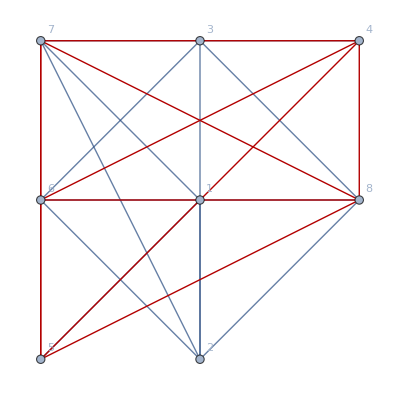

```mathematica
g=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->7,7<->8,8<->1,
1<->5,1<->6,1<->7,
2<->6,2<->7,2<->8,
3<->6,3<->7,3<->8,
4<->6,4<->7,4<->8,
5<->7,5<->8,
6<->8

}, VertexLabels->"Name", GraphLayout->"DiscreteSpiralEmbedding",
GraphHighlight->EdgeList[CompleteGraph[5]]/. {1->7,2->8,3->6}]
```

```mathematica
LayeredDigraphEmbedding
```

```mathematica
FindClique[g,{5},All]
```

{{4,5,6,7,8},{3,4,6,7,8},{2,3,6,7,8},{1,5,6,7,8},{1,2,6,7,8}}

```mathematica
Roots[ChromaticPolynomial[g,x]==0,x]
```

x==0||x==4-ⅈ||x==4+ⅈ||x==1||x==2||x==3||x==4||x==5

```mathematica
Factor[ChromaticPolynomial[g,x]]
```

(-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x (17-8 x+x^2)

```mathematica
ChromaticPolynomial[g,x]==0
```

-2040 x+5618 x^2-6137 x^3+3519 x^4-1160 x^5+222 x^6-23 x^7+x^8==0

```mathematica
formg=FindFullFormula[g]
```

{v1x2x3x4x5x6x7x8,v1x2x35x4x6x7x8,v1x25x3x4x6x7x8,v1x24x3x5x6x7x8,v1x24x35x6x7x8,v14x2x3x5x6x7x8,v14x2x35x6x7x8,v14x25x3x6x7x8,v13x2x4x5x6x7x8,v13x25x4x6x7x8,v13x24x5x6x7x8}

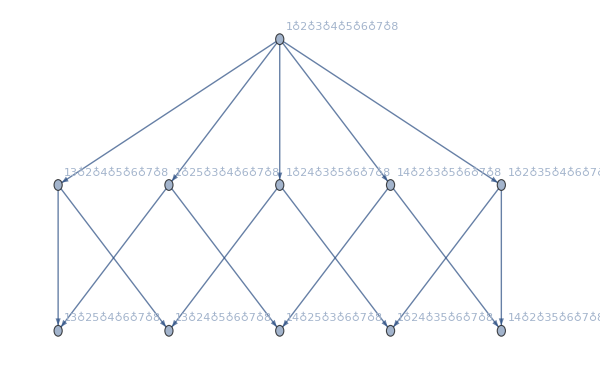

```mathematica
Graph[FormulaGraph[formg],AspectRatio->1/GoldenRatio,ImageSize->600]
```

```mathematica
GraphDistanceMatrix[g]//MatrixForm
```

(0 | 1 | 2 | 2 | 1 | 1 | 1 | 1
1 | 0 | 1 | 2 | 2 | 1 | 1 | 1
2 | 1 | 0 | 1 | 2 | 1 | 1 | 1
2 | 2 | 1 | 0 | 1 | 1 | 1 | 1
1 | 2 | 2 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0)

```mathematica
GraphDiameter[g]
```

2

```mathematica
GraphRadius[g]
```

1

```mathematica
GraphCenter [g]
```

{6,7,8}